```mathematica
AppendTo[$Path,NotebookDirectory[]];
Needs["PenroseTilingFunctions`"]
```

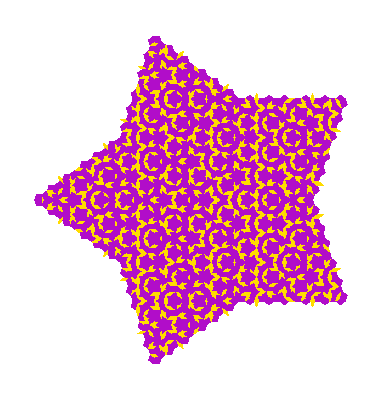

```mathematica
See@FullInflate[starseed,6]
```

```mathematica
See@{unitfat}
```

```mathematica
Coor/@Δ/@{unitfat}
```

{{{-0.809017,0},{0.809017,0},{1.11022×10^-16,0.587785}}}

```mathematica
Graphics[Line[{{-0.8090169943749475,0},{0.8090169943749475,0}}]]
```

```mathematica
Kites[{{A_,B_,C_},t_}]:=
If[t=="fat",Line[Coor[{A,B}]],Line[Coor[{B,C}]]]
```

```mathematica
{unitfat}
```

{{{-0.809017,0.809017,1.11022×10^-16+0.587785 ⅈ},fat}}

```mathematica
Coor[{-0.8090169943749475,0.8090169943749475}]
```

{{-0.809017,0},{0.809017,0}}

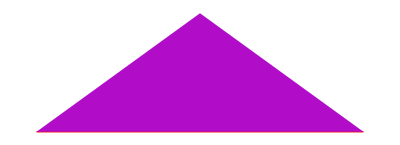

```mathematica
Show[Graphics[{Thick,Red,Kites[unitfat]}],See@{unitfat}]
```

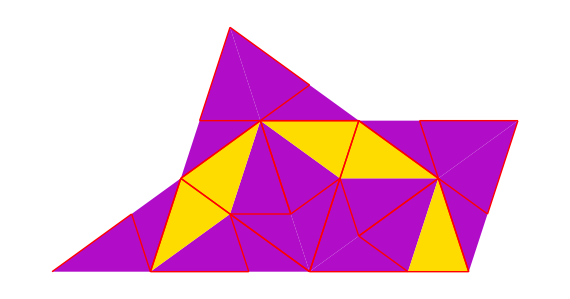

```mathematica
Show[See@Inflate[starseed,1],Graphics[{Red,Thick,Kites/@Inflate[starseed,2]}]]
```

```mathematica
KiteFill[{{A_,B_,C_},t_}]:={A,C,A+(A-B)(1-ϕ)}
```

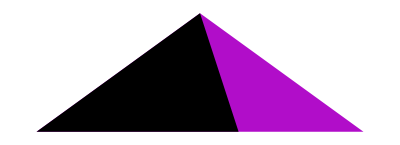

```mathematica
Show[{See@{unitfat},Graphics[Triangle/@Coor/@KiteFill/@{unitfat}]}]
```

```mathematica
??FatInflate
```

Inflation Rules for fat triangles

FatInflate[{{a_,b_,c_},f_}]:=Block[{d=a+(c-a)/ϕ,e=a+(b-a)/ϕ},{Fat[{e,a,d}],Skinny[{d,c,e}],Fat[{b,c,e}]}]

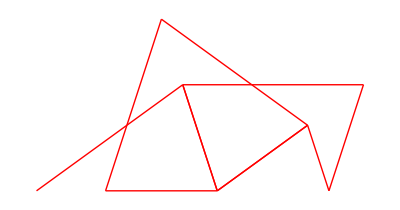

```mathematica
Graphics[{Red,Thick,Kites/@Inflate[starseed,1]}]
```

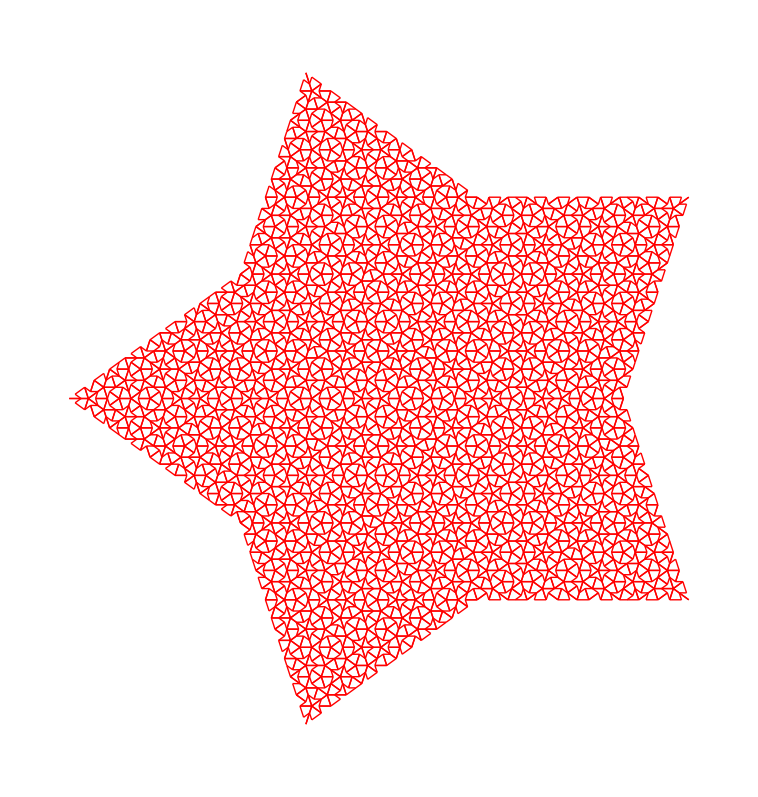

```mathematica
Graphics[{Red,Thick,Kites/@AddConj[Inflate[starseed,7]]}]
```

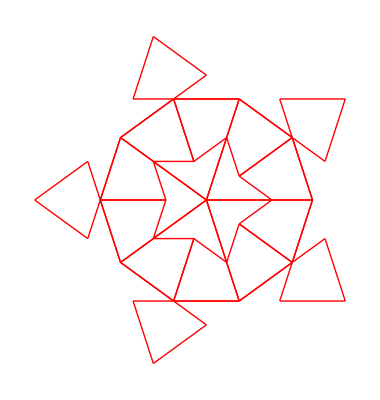
```mathematica
-Graphics-3
```

3 -Graphics-

```mathematica
??FullInflate
```

Inflates, Conjugates, Culls, and Converts to Rhombs

FullInflate[seed_,n_]:=Rhomb/@Cull[AddConj[Inflate[seed,n]]]